Final Project
Math 6380J: A Mathematical Introduction to Data Analysis (数据分析的数学导论)

by HUANG, Yiyi (20391572), yhuangcm@connect.ust.hk

I analyzed Jiashun Jin’s data on Coauthorship and Citation Networks for Statisticians. All was done independently.
First, adjacency matrix was  generated from the file “Jiashun/coauthorship/coauthorAdjThreshGiant.txt “. Then I drew adjacency graph according to the matrix. Vertices (authors) were clustered into several groups (communities) based on connectivity. At the same time, based on the number of coauthored papers (or say, degree of the vertex), “ top “  authors were found globally and in each group, respectively.
The same analysis was applied to the other two data files. Here are Mathematica codes and results.

The data used is ./Documents/data_analysis/Jiashun/coauthorship/coauthorAdjThreshGiant.txt

Here are adjacency graph without numbers, with numbers and with names, respectively

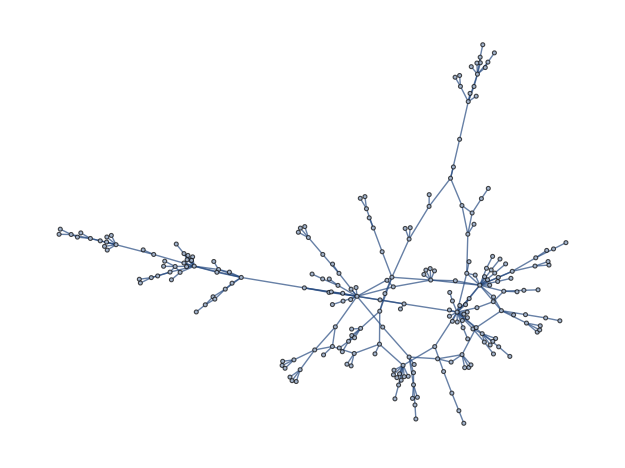

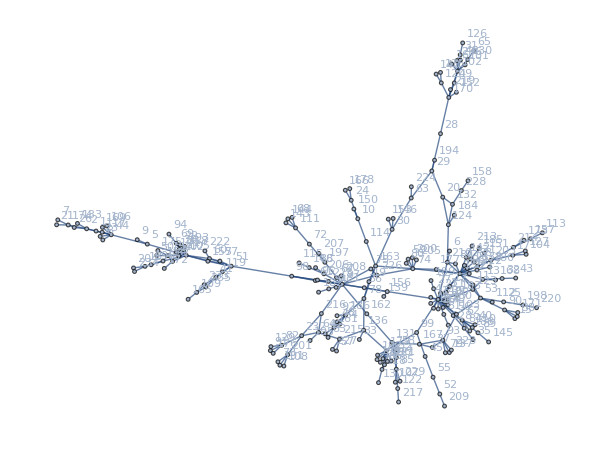

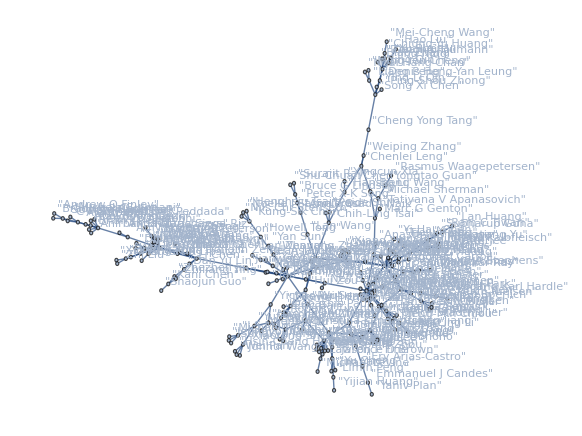

"Top" 10 authors (from less to greater) are:

{"Hans-Georg Muller","Hongtu Zhu","David Dunson","Hua Liang","Jing Qin","T Tony Cai","Joseph G Ibrahim","Jianqing Fan","Raymond J Carroll","Peter Hall"}

Cluster all authors into groups based on connectivity

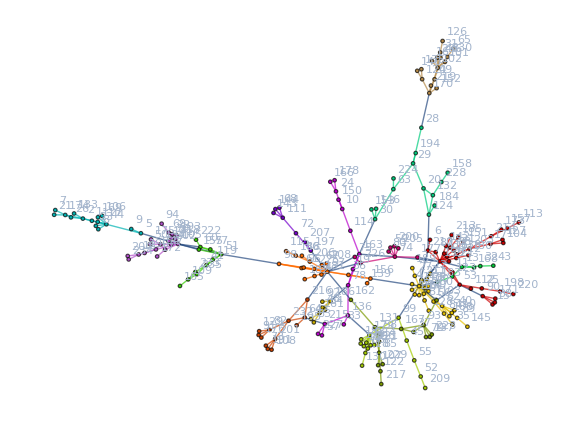

-Graphics-

Group 1

{"Anastasios A Tsiatis","Arnab Maity","Bin Nan","Byeong U Park","Enno Mammen","Jeffrey D Hart","Jeffrey S Morris","Jianhua Z Huang","John D Kalbfleisch","Kyusang Yu","Lan Huang","Lan Zhou","Menggang Yu","Naisyin Wang","Nilanjan Chatterjee","Philip J Brown","Ram C Tiwari","Raymond J Carroll","Subharup Guha","Tailen Hsing","Tiejun Tong","Wolfgang Karl Hardle","Xihong Lin","Yanyuan Ma","Yehua Li","Yi-Hau Chen","Yi Li","Ying Chen","Ying Wei","Yuedong Wang"}

"Top" 2 authors in Group 1

{"Enno Mammen","Raymond J Carroll"}

Group 2

{"Alexander Meister","Amnon Neeman","Aurore Delaigle","Celine Vial","Ci-Ren Jiang","D M Titterington","Damla Senturk","Fang Yao","Hans-Georg Muller","Hugh Miller","Ingrid Van Keilegom","Jane-Ling Wang","Jeng-Min Chiou","Jing-Hao Xue","Kehui Chen","Michael G Akritas","Pai-Ling Li","Peihua Qiu","Peter Hall","Richard Samworth","Ryan T Elmore","Tung Pham","Ulrich Stadtmuller","Vladimir Spokoiny","Yao-Ban Chan"}

"Top" 2 authors in Group 2

{"Hans-Georg Muller","Peter Hall"}

Group 3

{"Bing-Yi Jing","Bradley S Peterson","Debajyoti Sinha","Dipak K Dey","Heping Zhang","Hongtu Zhu","Jian Shi","Joseph G Ibrahim","Ming-Hui Chen","Niansheng Tang","Qi-Man Shao","Stuart R Lipsitz","Sungduk Kim","Wang Zhou","Weili Lin","Xiaoyan Shi","Xin-Bing Kong","Yimei Li","Zhi Liu"}

"Top" 2 authors in Group 3

{"Hongtu Zhu","Joseph G Ibrahim"}

Group 4

{"Chunming Zhang","Clifford Lam","Haibo Zhou","Heng Peng","Jean Jacod","Jiancheng Jiang","Jianqing Fan","Jianwen Cai","Lan Zhang","Neil Bathia","Per Aslak Mykland","Qiwei Yao","Tao Huang","Tao Yu","Yacine Ait-Sahalia","Yang Feng","Yingying Fan"}

"Top" 2 authors in Group 4

{"Qiwei Yao","Jianqing Fan"}

Group 5

{"Bee Leng Lee","Cun-Hui Zhang","Guang Cheng","Huiliang Xie","Jason P Fine","Jian Huang","Joel L Horowitz","Jun Yan","Limin Peng","Michael R Kosorok","Minggen Lu","Rui Song","Shuangge Ma","Yijian Huang","Ying Zhang","Yu Cheng"}

"Top" 2 authors in Group 5

{"Michael R Kosorok","Jian Huang"}

Group 6

{"Biao Zhang","Chiung-Yu Huang","Dean A Follmann","Denis Heng-Yan Leung","Hao Liu","Jing Ning","Jing Qin","Liang Peng","Mei-Cheng Wang","Ming-Yen Cheng","Ngai Hang Chan","Ping-Shou Zhong","Song Xi Chen","Ying-Li Qin","Yu Shen","Zonghui Hu"}

"Top" 2 authors in Group 6

{"Song Xi Chen","Jing Qin"}

Group 7

{"Abel Rodriguez","Alan E Gelfand","Amy H Herring","Andrew O Finley","Anirban Bhattacharya","Anna Maria Siega-Riz","Bradley P Carlin","Brian J Reich","C F Sirmans","David Dunson","Ju-Hyun Park","Lawrence Carin","Michele Guindani","Shyamal Das Peddada","Sudipto Banerjee"}

"Top" 2 authors in Group 7

{"Alan E Gelfand","David Dunson"}

Group 8

{"David L Donoho","Emmanuel J Candes","Ery Arias-Castro","Harrison H Zhou","Hongzhe Li","Jiashun Jin","Lawrence D Brown","Lie Wang","Mark G Low","Michael Levine","T Tony Cai","Weidong Liu","Wenguang Sun","X Jessie Jeng","Yaniv Plan"}

"Top" 2 authors in Group 8

{"Lawrence D Brown","T Tony Cai"}

Group 9

{"Annie Qu","Bo Kai","Bruce G Lindsay","Christina Kendziorski","Grace Wahba","Hui Zou","Lan Wang","Ming Yuan","Peter X-K Song","Runze Li","Shu-Chuan Chen","Surajit Ray","Yi Lin","Yongho Jeon"}

"Top" 2 authors in Group 9

{"Yi Lin","Runze Li"}

Group 10

{"Bo Li","Cheng Yong Tang","Chenlei Leng","Chih-Ling Tsai","Hansheng Wang","Marc G Genton","Michael Sherman","Peide Shi","Prasad A Naik","Rasmus Waagepetersen","Tatiyana V Apanasovich","Weiping Zhang","Yingcun Xia","Yongtao Guan"}

"Top" 2 authors in Group 10

{"Chih-Ling Tsai","Marc G Genton"}

Group 11

{"Hao Helen Zhang","Hsin-Cheng Huang","J S Marron","Jeongyoun Ahn","Junhui Wang","Michael J Todd","Sungkyu Jung","Wei Pan","Wenbin Lu","Xiaotong Shen","Yichao Wu","Yufeng Liu"}

"Top" 2 authors in Group 11

{"Xiaotong Shen","Yufeng Liu"}

Group 12

{"Dan Yu Lin","Donglin Zeng","Guosheng Yin","Hui Li","Kani Chen","Li Chen","Qingxia Chen","Shaojun Guo","Ying Yuan","Zhezhen Jin","Zhiliang Ying"}

"Top" 2 authors in Group 12

{"Guosheng Yin","Donglin Zeng"}

Group 13

{"Guohua Zou","Hua Liang","Huazhen Lin","Hulin Wu","Suojin Wang","Xiang Liu","Xinyu Zhang","Yong Zhou"}

"Top" 2 authors in Group 13

{"Yong Zhou","Hua Liang"}

Group 14

{"Daniela M Witten","Debashis Paul","Eric Bair","Jacob Bien","Jerome H Friedman","Robert J Tibshirani","Trevor J Hastie"}

"Top" 2 authors in Group 14

{"Robert J Tibshirani","Trevor J Hastie"}

Group 15

{"Henghsiu Tsai","Howell Tong","Kung-Sik Chan","Nils Chr Stenseth","Noelle I Samia","Wenyang Zhang","Yan Sun"}

"Top" 2 authors in Group 15

{"Wenyang Zhang","Kung-Sik Chan"}

Group 16

{"Bani Mallick","Chris C Holmes","David A Stephens","Malay Ghosh","Shubhankar Ray","Tapabrata Maiti"}

"Top" 2 authors in Group 16

{"Tapabrata Maiti","Bani Mallick"}

Group 17

{"Bent Nielsen","D Kuang","Jens Perch Nielsen","Stefan Sperlich"}

"Top" 2 authors in Group 17

{"D Kuang","Jens Perch Nielsen"}

```mathematica
data1="./Documents/data_analysis/Jiashun/coauthorship/coauthorAdj.txt";
data2="./Documents/data_analysis/Jiashun/coauthorship/coauthorAdjGiant.txt";
data3="./Documents/data_analysis/Jiashun/coauthorship/coauthorAdjThreshGiant.txt";
names2="./Documents/data_analysis/Jiashun/coauthorship/authorListCoauthorGiant.txt";
names3="./Documents/data_analysis/Jiashun/coauthorship/authorListCoauthorThreshGiant.txt";
data=data3;
names=names3;
Style["The data used is "<>data,Blue,Large]
adjMatrix=ReadList[data,Number ,RecordLists->True];
nameList=ReadList[names,String];
(*Dimensions[adjMatrix]
Dimensions[nameList]
adjMatrix[[1]]*)
Style["Here are adjacency graph without numbers, with numbers and with names, respectively", Blue, Large]
adjGraphPoint=AdjacencyGraph[adjMatrix]
adjGraphNumber=AdjacencyGraph[adjMatrix,VertexLabels->"Name"]
adjGraphName=AdjacencyGraph[adjMatrix,VertexLabels->Table[i->nameList[[i]],{i,1,Length[nameList]}]]
adjGraph=adjGraphNumber;
Style["\"Top\" 10 authors (from less to greater) are: ", Blue, Large]
 degree=DegreeCentrality[adjGraph];
(*Sort[degree]*)
(* top n, from less to greater *)
Ordering[degree,-10];
nameList[[%]]
groups=FindGraphCommunities[adjGraph];
(*Dimensions[groups]*)
Style["Cluster all authors into groups based on connectivity ",Blue,Large]
HighlightGraph[adjGraph,Subgraph[adjGraph,#]& /@groups]
CommunityGraphPlot[adjGraph,groups]
Table[
Print@Style["Group "<>ToString[j],Magenta,Large];
Print[nameList[[groups[[j]] ]]];
Print[Style["\"Top\" 2 authors in Group "<>ToString[j],Orange,Medium]];
degreej=degree[[groups[[j]]]];
groupTopIndex=Ordering[degreej,-2];
groupTop=groups[[j]][[groupTopIndex]];
Print[nameList[[groupTop]]],
{j,1,Length[groups]}];
```

The data used is ./Documents/data_analysis/Jiashun/coauthorship/coauthorAdjGiant.txt

Here are adjacency graph without numbers, with numbers and with names, respectively

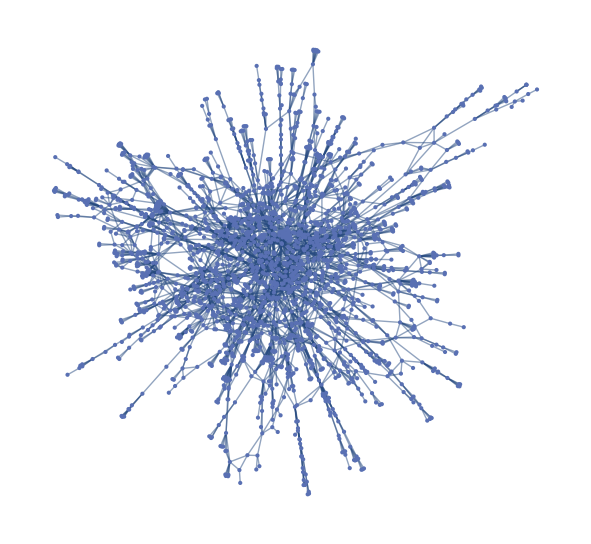

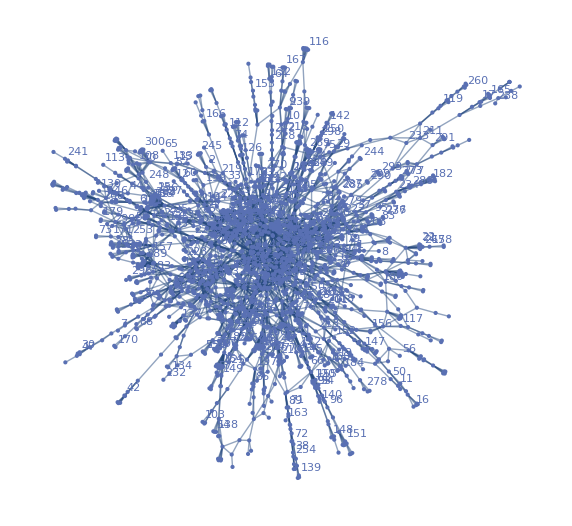

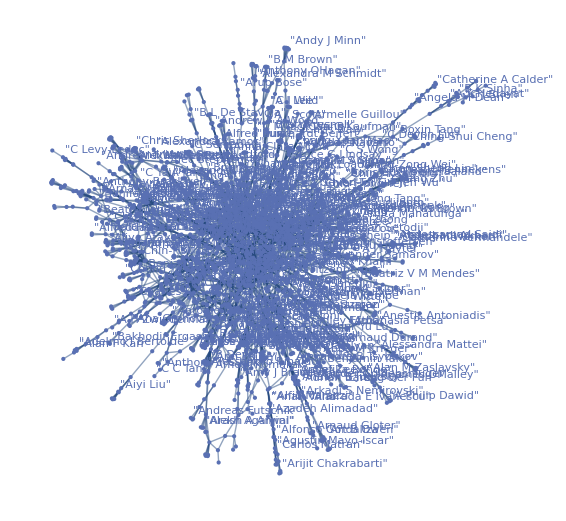

"Top" 10 authors (from less to greater) are:

{"Ciprian M Crainiceanu","Holger Dette","James O Berger","Lixing Zhu","Hongtu Zhu","David Dunson","Jianqing Fan","Joseph G Ibrahim","Raymond J Carroll","Peter Hall"}

Cluster all authors into groups based on connectivity

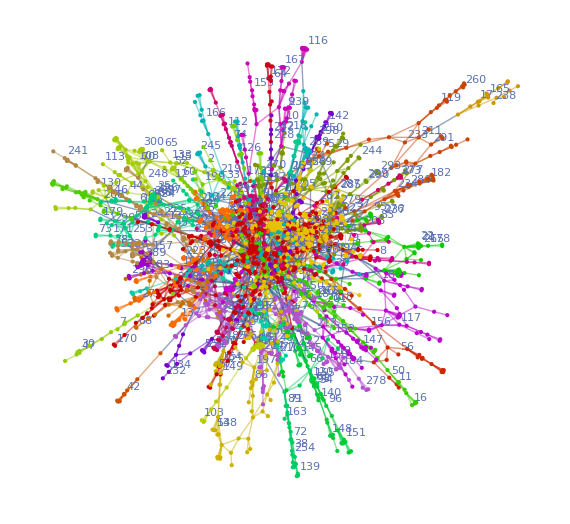

-Graphics-

Group 1

{"Alan H Welsh","Alexandre Rodrigues","Amanda S Hering","Ana-Maria Staicu","Andre Lucas","Anouar El Ghouch","Anthony C Hart","Arnab Maity","Arnost Komarek","Barry Rowlingson","Bent Nielsen","Bernd Fitzenberger","Bhramar Mukherjee","Bin Nan","Bing Li","Bo Kai","Bo Li","Brian S Caffo","Byeong U Park","C A Field","C Messan Setodji","Carlos Acuna","Carmen Cadarso-Suarez","Caroline Beunckens","Catherine Schairer","Celia Byrne","Changliang Zou","Chenlei Leng","Chi-Lun Cheng","Chih-Ling Tsai","Chong-Zhi Di","Christel Faes","Christian Peter Klingenberg","Christine H Muller","Christoph Rothe","Christopher J Nachtsheim","Chunfeng Huang","Chunlei Ke","Ciprian M Crainiceanu","Colin M Beale","Craig W Hendrix","Cristina Sotto","D Kuang","David Ruppert","David Y Pee","Dennis Cook","Dimitris Rizopoulos","Donghoh Kim","Douglas G Simpson","E Ferreira","Efi S Antoniou","Emily L Kang","Emmanuel Lesaffre","Enno Mammen","Fauzia Paize","Francesca Chiaromonte","Fredrik A Dahl","Galin L Jones","Ganggang Xu","Gardar Johannesson","Geert Molenberghs","Geert Verbeke","Gerda Claeskens","Gilbert Mackenzie","Gunnhildur Hognadottir Steinbakk","Guodong Li","H Thijs","Hansheng Wang","Haobo Ren","Heather Spencer Feigelson","Helena Geys","Hongyuan Zha","Hua Liang","Huajun Ye","Huiyan Sang","Il Do Ha","Ingrid Van Keilegom","Ivan Mizera","J L Scealy","J T Ormerod","Jacques Benichou","Jae Keun Yoo","James A Calvin","James M Flegal","James R Robins","Jeffrey D Hart","Jeng-Min Chiou","Jens Perch Nielsen","Jian Shi","Jianhua Z Huang","Jianxin Pan","Jinbo Chen","Joanne R Lupton","John P Buonaccorsi","John Staudenmayer","Josue G Martinez","Jouni Kuha","Jussi Klemela","Kam-Chuen Yuen","Kevin K Dobbin","Kyusang Yu","Lan Wang","Lan Xue","Lan Zhou","Leopold Simar","Lexin Li","Li Wang","Lianfen Qian","Lijian Yang","Lijuan Deng","Liliana Forzani","Linxu Liu","Liping Zhu","Liqiang Ni","Liugen Xue","Lixing Zhu","Louis Ferre","Lu Lin","Lynda D Lisabeth","M P Wand","Maengseok Noh","Marc Aerts","Marc G Genton","Margaret R Karagas","Maria Dolores Martinez Miranda","Maria Jose Lombardia","Martica Hall","Martin Hillebrand","Meeyoung Hong","Melanie Schienle","Mi-Ja Woo","Michael G Akritas","Michael G Kenward","Michael Sherman","Michelle Stanton","Min Hee Kim","Min Kyung Kim","Minge Xie","Mitchell H Gail","Mohsen Pourahmadi","Monica Cano","Murali Haran","N Papadatos","Naiping Liu","Naisyin Wang","Nancy D Turner","Naomi Altman","Naresh M Punjabi","Nilanjan Chatterjee","Nils Lid Hjort","Noel Cressie","Norman E Breslow","Olga Y Savchuk","Oliver B Linton","Pai-Ling Li","Peide Shi","Pengjie Dai","Peter J Diggle","Prasad A Naik","Qihua Wang","R Dennis Cook","R J Buchanan","R L Eubank","Rajeev Ayyagari","Rajita Sinha","Rasmus Waagepetersen","Raymond J Carroll","Reinhard Furrer","Robert T Krafty","Roger Koenker","Ronald Neath","Ronghua Luo","Ross Iaci","Runze Li","Russ Hauser","Ryan Janicki","Sally W Thurston","Samiran Sinha","Samuel Muller","Sanford Weisberg","Sara van de Geer","Sarah J Ratcliffe","Seok-Oh Jeong","Sheng Luo","Simon J Sheather","Sioban D Harlow","Songqiao Wen","Stefan Sperlich","Sung-Cheol Yun","Suojin Wang","Szymon Borak","T N Sriram","Tae Yoon Kim","Tailen Hsing","Tao Wang","Tatiyana V Apanasovich","Thomas A Louis","Thomas T Ten Have","Tianle Hu","Tiejun Tong","Tor D Tosteson","Tyler J Vanderweele","Uta Pigorsch","Vadim M Zipunnikov","Veerabhadran Baladandayuthapani","W L Xu","W Ryan Diver","Wai Keung Li","Weiping Zhang","Wensheng Guo","Winfried Stute","Wolfgang Karl Hardle","Xia Cui","Xiang Liu","Xiangrong Yin","Xiaobo Ding","Xihong Lin","Xin Chen","Y Munoz Maldonado","Yaning Yang","Yanyuan Ma","Ye Shen","Yehua Li","Yi-Hau Chen","Ying Chen","Ying Sun","Ying Wei","Yingxing Li","Yiyun Zhang","Yongtao Guan","Yongwu Shao","Young Kyung Lee","Youngjo Lee","Yu-Jen Cheng","Yuanqing Ye","Yuedong Wang","Yuexiao Dong","Yulia V Marchenko","Yun Sam Chong","Yunling Du","Zengri Wang","Zhangsheng Yu","Zhen Pang","Zhenghui Feng","Zhihua Su","Zhijie Xiao","Zonghui Hu"}

"Top" 2 authors in Group 1

{"Lixing Zhu","Raymond J Carroll"}

Group 2

{"A B Kristoffersen","A Galichon","Abhyuday Mandal","Adonis Yatchew","Alan T K Wan","Alexander Meister","Alexandre Belloni","Alysha M De Livera","Amnon Neeman","Andrew P Robinson","Andrew V Carter","Aurore Delaigle","Baiqi Miao","Bee Leng Lee","Bitao Liu","Brent A Johnson","Brian S Yandell","Chengcheng Hu","Chia-Hung Yen","Chien-Tai Lin","Chunfang Jin","Chunming Zhang","Ci-Ren Jiang","Clifford Lam","Cun-Hui Zhang","Dacheng Xiu","Damla Senturk","Dan Yu Lin","Dandan Liu","Daniel Molefe","David Pollard","David V Glidden","Deli Wang","Dixin Zhang","Do-Hwan Park","Dong Chen","Donglin Zeng","Dongsheng Tu","Efang Kong","Eitan Greenshtein","Eric Johnson","F Ferraty","Fang Yao","Fengchang Lin","Fengrong Wei","Flavio Ziegelmann","Fuqing Gao","Fushing Hsieh","Gauri Sankar Datta","Guohua Zou","Guosheng Yin","Guoying Li","Gustavo Didier","Haibo Zhou","Hans-Georg Muller","Harrison H Zhou","Heng Peng","Hong-Bin Fang","Hong Ooi","Hong Zhang","Hongqi Xue","Hongyu Miao","Hongyu Zhao","Hongzhe Li","Howell Tong","Hua-Hua Chang","Huazhen Lin","Hugh Miller","Hui Li","Huiliang Xie","Hulin Wu","I Fernandez-Val","Ibrahim Ahmad","Ilya Molchanov","J-H Jeong","J T Gene Hwang","James X Hu","Jane-Ling Wang","Jason P Fine","Jean Jacob","Jeff Racine","Jelena Bradic","Jialiang Li","Jian Huang","Jian Zou","Jiancheng Jiang","Jianguo Sun","Jianqing Fan","Jianwei Chen","Jianwen Cai","Jiashun Jin","Jiazhu Pan","Jichun Xie","Jin-Ting Zhang","Jinchi Lv","Jinfeng Xu","Jing Qiu","Jingran Sun","Jiying Yin","Joel A Dubin","Joel L Horowitz","Julian Z Wang","Jun Sheng","Jun Yan","Jyh-Shyang Wu","K F Lam","Kani Chen","Ke Yu","Kee-Hoon Kang","Kehui Chen","Kristine E Lee","Kun Chen","Kung-Sik Chan","Kwang Woo Ahn","L J Wei","Lan Kong","Lawrence D Brown","Li-Shan Huang","Li Chen","Liang Peng","Lie Wang","Lincheng Zhao","Liuquan Sun","Lop-Hing Ho","Lu-Hung Chen","Mark A Weaver","Mark G Low","Meng Mao","Michael C Minnotte","Michael Kosoy","Michael Levine","Michael R Kosorok","Michal Kulich","Ming-Tien Tsai","Ming-Yen Cheng","Mingjin Wang","Minjing Tao","Mohammad Hosseini-Nasab","Myung Hwan Seo","N Balakrishnan","Nader Ebrahimi","Neil Bathia","Nicolas Verzelen","Nils Chr Stenseth","Ning Hao","Nivedita V Nadkarni","Noelle I Samia","P Vieu","Pang Du","Peihua Qiu","Peter Hall","Philip W Davidson","Pranab K Sen","Qi Li","Qiwei Yao","Ralph D Snyder","Reza Pakyari","Rob J Hyndman","Robert L Winkler","Ronald E Gangnon","Rong Tang","Rui Song","Ruoqing Zhu","Ryan T Elmore","S Kang","S S J Wang","Sandy Clarke","Shaojun Guo","Shuangge Ma","Sin-Ho Jung","Sittisak Leelahanon","Sokbae Lee","Spiridon Penev","T Tony Cai","Tao Huang","Tao Lu","Tao Yu","Thomas D Cook","Tiefeng Jiang","Tsz Ho Yim","Tung Pham","Ulrich Stadtmuller","Victor Chernozhukov","Vladimir S Troynikov","Weidong Liu","Weiwei Wang","Wenbin Lu","Wenguang Sun","Wenhua Jiang","Wenjing Yang","Wenwen Tao","Wenyang Zhang","X Jessie Jeng","Xi Luo","Xiao-Hua Zhou","Xiaojing Wang","Xiaoping Xu","Xin Qi","Xin Tong","Xingqiu Zhao","Xingwei Tong","Xinyu Zhang","Xinyuan Song","Xueli Liu","Yacine Ait-Sahalia","Yair Goldberg","Yan Sun","Yanan Fan","Yang Feng","Yao-Ban Chan","Yazhen Wang","Yi-Kuan Tseng","Yi Chai","Yichao Wu","Ying Bai","Yingcun Xia","Yingqi Zhao","Yingying Fan","Yingying Li","Yong Zhou","Yongcheng Qi","You-Jun Yang","Youngki Shin","Yu Cheng","Yuan Jiang","Yuanyuan Lin","Yue S Niu","Yuh-Shan Jou","Yuhyun Park","Zhengyan Lin","Zhezhen Jin","Zhi Wei","Zhigang Zhang","Zhigen Zhao","Zhiliang Ying","Zhiyi Zhang","Zongwu Cai"}

"Top" 2 authors in Group 2

{"Jianqing Fan","Peter Hall"}

Group 3

{"A Mallik","Adam J Rothman","Adi F Gazdar","Ali Ekici","Ali Shojaie","Armin Schwartzman","B Sigal","Benjamin Yakir","Benoit R Masse","Bodhisattva Sen","Bowei Xi","Bradley Efron","Bryan E Shepherd","C Y Wang","Catherine A Sugar","Cheng-Der Fuh","Christian Bressen Pipper","Christina Kendziorski","Chun Li","Daniela M Witten","David M Zucker","David Siegmund","Debashis Paul","Donna P Ankerst","Earl Lawrence","Elizaveta Levina","Els Goetghebeur","Emilio Seijo","Eric Bair","Eric J Tchetgen","F Gosselin","F Zoe Moodie","Gareth M James","Genevera I Allen","George Michailidis","Haiqun Lin","Hajime Uno","Hanlee Ji","Hock Peng Chan","Holly Janes","Hui Zou","Ian W McKeague","Inchi Hu","Jacob Bien","Jacob von Bornemann Hjelmborg","Jacqueline J Meulman","James Y Dai","Jayanta Pal","Jerome H Friedman","Jessica Minnier","Ji Zhu","Jian Guo","Jianrong Wu","Jianxin Shi","Jie Peng","Jing Wang","Jinglai Shen","John D Storey","Jonathan E Taylor","Jun-Z Li","K Shafie","Keith J Worsley","Keith Knight","Keyur H Desai","Krista Fischer","Li Hsu","Lihong Qi","Lin S Chen","Lingzhou Xue","Lu Tian","M A Goldwasser","Malka Gorfine","Margaret Sullivan Pepe","Mario Mateo","Martin A Lindquist","Mary W Redman","Matthew Walker","Mee Young Park","Mei-Jie Zhang","Mette Gerster","Michael Saunders","Michael Woodroofe","Ming Yuan","Moulinath Banerjee","Mu Zhu","N Chamandy","Nam Hee Choi","Nancy Ruonan Zhang","Narayan Shivapurkar","Nengfeng Zhou","Noah Simon","Pei Wang","Peter B Gilbert","Peter Radchenko","Probal Chaudhuri","Qing Mai","Rahul Mazumder","Renato Monteiro","Robert F Dougherty","Robert J Tibshirani","Robert Jarrow","Ross L Prentice","Runlong Tang","Ryan J Tibshirani","Saharon Rosset","Sarat C Dass","Scott D Solomon","Siji Wang","Song Yang","Steven L Scott","Stijn Vansteelandt","Sylvie Goetgeluk","Thomas A Gerds","Thomas H Scheike","Thomas Lumley","Tianxi Cai","Tina Kold Jensen","Torben Martinussen","Trevor J Hastie","Tyler J VanderWeele","Vijayan N Nair","W J Hall","Walter F Mascarenhas","Wayne C Levy","Wei-Liem Loh","William Li","Xiao Wang","Yan Lan","Yan Yu","Yannis Jemiai","Yanqing Sun","Ying Huang","Yingye Zheng","Yuval Nardi","Zhaosong Lu","Ziding Feng"}

"Top" 2 authors in Group 3

{"Robert J Tibshirani","Ji Zhu"}

Group 4

{"A D Tsodikov","Amgen Research Group","Ananya Roy","Andrei Y Yakovlev","Antonio Lijoi","Ashutosh Tewari","Bani Mallick","Bichun Ouyang","Bradley S Peterson","Brent A Coull","Brisa N Sanchez","C G Wager","Cassandra Arroyo","Chang-Yung Yu","Charles R G Guttmann","Chien-Jen Chen","Ching-Ti Liu","Christine G Elsik","Chuanhai Liu","Colin Hall","D Azriel","Dalho Kim","Daniel B Rowe","David B Dahl","Debajyoti Sinha","Debashis Ghosh","Diane Lambert","Dinggang Shen","Dipak K Dey","Duchwan Ryu","E Andres Houseman","Emily C Martin","Eric V Slud","Esben Budtz-Jorgensen","Eugenio Regazzini","Faming Liang","Feng Guo","Giovanni Peccati","Heping Zhang","Hong-Tu Zhu","Hongtu Zhu","Hongxiao Zhu","Hongyu An","Howard Hu","Howard L Weiner","Hyunsoon Cho","Igor Prunster","Ilenia Epifani","James P Shine","Jeffrey Lieberman","Jeffrey S Morris","Jerry W Tsai","Jian Zhang","John Allen Logan","John H Gilmore","Joseph G Ibrahim","Kent E Holsinger","Knashawn H Morales","Kristin P Lennox","Kyounghwa Bae","L Garry Adams","Lisa M Chung","Louise M Ryan","Luis E Nieto-Barajas","M Brent McHenry","Mahlet G Tadesse","Malay Ghosh","Marina Vannucci","Martin Styner","Micha Mandel","Michael A Newton","Ming-Hui Chen","N Lange","Naijun Sha","Niansheng Tang","Nikolay M Yanev","Peter D Hoff","Philip J Brown","Pierpaolo De Blasi","Qingxia Chen","R Fluss","Rajesh Talluri","Ramses H Mena","Rebecca A Betensky","Richard Herrick","Rui Feng","Sangeeta Khare","Sara D Lawhon","Shubhankar Ray","Sikyum Lee","Sinae Kim","Soma S Dhavala","Sounak Chakraborty","Stefano Favaro","Stephen G Walker","Steven E Lipshultz","Steven L Gortmaker","Stuart R Lipsitz","Sujay Datta","Sungduk Kim","Susan A Gauthier","Tapabrata Maiti","Thomas S Shively","Thomas W Sager","Trevor J Sweeting","Vessela K Stoimenova","Wei Gao","Weili Lin","Wensheng Zhu","Xiaohui Wang","Xiaoyan Shi","Xueqin Wang","Y Rinott","Yashen Chen","Yasheng Chen","Yimei Li","Ying Yuan","Yuan Ji","Yunxiao He","Yvonne Pittelkow"}

"Top" 2 authors in Group 4

{"Hongtu Zhu","Joseph G Ibrahim"}

Group 5

{"Abdus S Wahed","Adarsh Joshi","Anastasios A Tsiatis","Andrew S Allen","Biao Zhang","Bob Zhong","Boris Buchmann","Brett Presnell","C Hendricks Brown","C S Wong","Chen-Pin Wang","Cheng Yong Tang","Ching-Kang Ing","Ching-Zong Wei","Chiung-Yu Huang","Cindy Long Yu","Cyrus Mehta","David Rossell","Dean A Follmann","Denis Heng-Yan Leung","Dennis D Boos","Dennis Young","Dong Li","Dong Wang","Estate V Khmaladze","Fang Fang","Fei Zou","Feifang Hu","Fred A Wright","Gilbert J Cote","Glen A Satten","Graciela Boente","Guozhi Gao","Hanwen Huang","Hao Liu","Hengjian Cui","Hira L Koul","Hongjian Zhu","Hongwen Guo","Howard D Bondell","Huixia Judy Wang","Hyokyoung Grace Hong","Irene Gijbels","Jianhua Hu","Jianhui Zhou","Jing Ning","Jing Qin","Jiti Gao","Joseph P Costantino","Jun-Iowa Li","Jun Shao","Kai W Ng","Karen Bandeen-Roche","Ke Zhu","Leonard A Stefanski","Li-Xin Zhang","Marek Omelka","Marie Davidian","Mendel Fygenson","Mi-Ok Kim","Michael McAleer","Ming Li","Nan Lin","Ngai Hang Chan","Noel Veraverbeke","P L Kam","Ping-Shou Zhong","Quan Hong","Ralf Krahe","Rudolf Grubel","Seunggeun Lee","Shein-Chung Chow","Shiqing Ling","Siu Hung Cheung","Somnath Datta","Song Xi Chen","Steven J Novick","Tigran Markaryan","Valen E Johnson","Vincent T Mule Jr","Viswanath Devanarayan","Wai Sum Chan","Weihua Cao","Weixing Song","Wentao Feng","William F Rosenberger","Wing K Fung","Xianzheng Huang","Xiaomin Lu","Xingdong Feng","Xinxin Yu","Xuming He","Yevgen Tymofyeyev","Yijun Zuo","Ying-Li Qin","Yonghee Lee","Yu Shen","Yujun Wu","Yunming Mu","Yunwen Yang","Zhongyi Zhu"}

"Top" 2 authors in Group 5

{"Song Xi Chen","Xuming He"}

Group 6

{"A Guillin","Alejandro Cruz-Marcelo","Antoine Chambaz","Barry M Lesht","Billy Amzal","Brunero Liseo","Bruno Sanso","C Levy-Leduc","Christian P Robert","Christopher A Bush","Christopher Morrell","Chun-Lung Su","Chunjie Wu","D M Titterington","Daniel Zantedeschi","David B Matchar","David J Schwab","David M Higdon","Dmitry Beletsky","Donatello Telesca","E Moulines","Edwin S Iversen Jr","eric Moulines","Eric Moulines","Eric Parent","Ethan B Anderes","Fernando A Quintana","Finn Lindgren","Francois Roueff","Frederic Y Bois","Gary L Rosner","Gersende Fort","Giovanni Parmigiani","Gregory P Samsa","H Boistard","Haavard Rue","Hae Kyung Im","Heidi W Ashih","Herbert K H Lee","Ingelin Steinsland","J-M Marin","J M Quashnock","Jean-Marie Cornuet","Jean-Michel Marin","Ji Meng Loh","Jimmy Olsson","Jing-Hao Xue","Johan Lindstrom","John C Liechty","Jonathan R Stroud","Jonathan Weinberg","Judith Rousseau","Juhee Lee","Katherine B Ensor","Kerrie Mengersen","Leah J Welty","Lionel Cucala","Lorenzo Trippa","Lurdes Y T Inoue","M S Taqqu","Maria De Iorio","Mark A Beaumont","Matthew A Taddy","Merrill W Liechty","Michael A Fligner","Michael L Stein","Nicholas G Polson","Nicolas Chopin","Offer Lieberman","Olivier Cappe","Pamela W Duncan","Paul Damien","Paula Diehr","Peter Lenk","Peter Muller","Pierre Priouret","Pilar L Iglesias","Ramon van Handel","Randal Douc","Rebecca A Hubbard","Ricardo T Lemos","Robert B Gramacy","Ruth Etzioni","Sara Martino","Sining Chen","Sofia Andersson","Steven N MacEachern","Sue Min Lai","Sveinung Erland","Tobias Ryden","V A Reisen","Weining Zhou","Wesley O Johnson","Xi Zhou","Youlan Rao","Z Harchaoui","Zhengyuan Zhu","Zhiyi Chi"}

"Top" 2 authors in Group 6

{"Christian P Robert","Peter Muller"}

Group 7

{"A C Davison","Abbas Khalili","Alessandro Tarozzi","Annie Qu","B L De Stavola","Baojiang Chen","Bin Zhu","Bruce G Lindsay","C Semadeni","Catherine Loader","Chang Xuan Mao","Changbao Wu","Christiana Kartsonaki","D A S Fraser","D Mastropietro","D R Cox","D V Hinkley","Denise Babineau","Douglas P Wiens","E Marras","Elena Stanghellini","Eunsik Park","Fei Wang","Frank Critchley","Gavin Shaddick","Giovanni M Marchetti","Grace Y Yi","Haihong Li","Hakbae Lee","Han Hong","Hanfeng Chen","Hee-Seok Oh","Hosik Choi","Howard M Sandler","J Jack Lee","Jaeyong Lee","James V Zidek","Jerald F Lawless","Jeremy M G Taylor","Ji-Ping Z Wang","Jiahua Chen","Jiawei Liu","John D Kalbfleisch","Jose Scheinkman","Kai-Sheng Song","Ke Yang","Ker-Ai Lee","Lajmi Lakhal-Chaieb","Lancelot F James","Lars Peter Hansen","Leilei Zeng","Lin Lu","Lu Wang","Luke Bornn","M-O Boldi","Man Yu Wong","Marc Fredette","Marianthi Markatou","Mary E Thompson","Mayer Alvo","Menggang Yu","N Reid","Nanny Wermuth","Paul Marriott","Peng Wang","Peng Zhang","Pengfei Li","Peter X-K Song","Qian M Zhou","Rafael Weissbach","Ramani S Pilla","Richard J Cook","Richard P Waterman","Shu-Chuan Chen","Shuanglin Zhang","Sunghoon Kwon","Surajit Ray","Ta-Hsin Li","Ting Zhang","Viktor Tsyrennikov","Wei Biao Wu","Weixin Yao","Wenqing He","Xianyang Zhang","Xiaofeng Shao","Xiaogang Wang","Xiaohong Chen","Xin Gao","Yanping Yi","Yanqin Fan","Yongdai Kim","Yongseok Park","Yukun Liu","Zehua Chen","Zhibiao Zhao","Zhijian Chen","Zhou Zhou"}

"Top" 2 authors in Group 7

{"Bruce G Lindsay","Peter X-K Song"}

Group 8

{"A N Pettitt","Adrian Baddeley","Ajay Jasra","Alec Stephenson","Alexandra Ramos","Alexandre Pintore","Alexandros Beskos","Andrew M Stuart","Andrew T Walden","Anthony Brockwell","Anthony W Ledford","Arnaud Doucet","Brian H Aukema","C Yau","Chao Yang","Chris C Holmes","Chris Sherlock","Christophe Andrieu","Claudia Tarantola","D S Choi","David A Stephens","David Lusseau","David Wyncoll","Dennis Prangle","Despina Vasileiou","E M Airoldi","Emma F Eastoe","Emma J McCoy","Eva B Vedel Jensen","Gareth Roberts","George Poyiadjis","Haonan Wang","Hyoung-Moon Kim","Ioannis Kontoyiannis","Jakob G Rasmussen","Janet E Heffernan","Jeffrey S Rosenthal","Jennifer L Wadsworth","Jesper Moller","Johanna Ziegel","John W Durban","Jonathan Tawn","Jun Zhu","K K Berthelsen","Karl-Anton Dorph-Petersen","Kenneth F Raffa","Kim Parsons","Konstantinos Kalogeropoulos","Loukia Meligkotsidou","M Hazelton","M Papathomas","Matthew P S Gander","Nial Friel","Niall M Adams","Nicholas A Heard","Ole F Christensen","Omiros Papaspiliopoulos","P Giudici","Patrick J Wolfe","Paul Fearnhead","Paul L Speckman","Paul M Thompson","Peter Clifford","Petros Dellaportas","Petter Wiberg","Philip S Hammond","Pierre Del Moral","R King","R Reeves","R Turner","Radu V Craiu","Roman Holenstein","Ross Corkrey","Simon J Godsill","Sofia C Olhede","Steve Brooks","Sumeetpal S Singh","Thierry Duchesne","Tingjin Chu","V G S Vasdekis","Wee-Jing Ng","Yvo Pokern","Zhen Liu"}

"Top" 2 authors in Group 8

{"Paul Fearnhead","Gareth Roberts"}

Group 9

{"Abba M Krieger","Alexander Samarov","Anestis Antoniadis","Arnaud Durand","Arthur Yu Lu","Athanasia Petsa","Bernard W Silverman","Celine Vial","Claudia Kirch","Daniel Yekutieli","Danilo Mercurio","David L Donoho","David S Stoffer","Denis Belomestny","Dimitris N Politis","Domenico Marinucci","Dominique Picard","Efstathios Paparoditis","Emmanuel J Candes","Ery Arias-Castro","Felix Abramovich","Gabriel Chandler","Gary Lorden","Gerard Kerkyacharian","Greg W Anderson","Guy P Nason","H-S Oh","Haeran Cho","Hannes Helgason","Hernando C Ombao","Hsiao-Yun Huang","Iain M Johnstone","Ion G Grama","J Sanderson","J Simoens","Jean-Francois Dupuy","Jean-Marc Freyermuth","Jens-Peter Kreiss","Jeremie Bigot","Jihong Chen","Jorg Polzehl","Karine Tribouley","Leen Slaets","M W Jones","Maarten Jansen","Marc Raimondo","Marianna Pensky","Mathilde Mougeot","Mauro Piccioni","Michael H Neumann","Ming Dai","Moshe Pollak","Mounir Mesbah","Ofer Zeitouni","Ori Rosen","P Baldi","Piotr Fryzlewicz","Rafal Kulik","Rainer Dahlhaus","Rainer von Sachs","Sally Wood","Sanat K Sarkar","Sebastien Gadat","Sebastien Van Bellegem","Stuart Barber","Suhasini Subba Rao","T J Heaton","Terence Tao","Thanh Mai Pham Ngoc","Theofanis Sapatinas","Tucker McElroy","V Delouille","Vadim Grinshtein","Vladimir Spokoiny","Wenge Guo","Wolfgang Polonik","Xiaoming Huo","Xuelei Ni","Yaniv Plan","Yoav Benjamini","Yulia Gavrilov"}

"Top" 2 authors in Group 9

{"Piotr Fryzlewicz","Iain M Johnstone"}

Group 10

{"A Jara","Abel Rodriguez","Abhishek Bhattacharya","Adrian Dobra","Aimee Zaas","Alan E Gelfand","Alex Lenkoski","Alfred Hero","Aliye Atay-Kayis","Amy H Herring","Andrew O Finley","Anirban Bhattacharya","Anna Maria Siega-Riz","Antonio Canale","Bala Rajaratnam","Beatrix Jones","Bernardo Colombo","Bo Cai","Bonifacio Salvador","Bradley P Carlin","Brian J Reich","C F Sirmans","Carlos M Carvalho","Chris Hans","Christopher Woods","Chuanhua Xing","Cristina Rueda","D Pati","David Dunson","David M Holland","David W MacFarlane","Freda Cooner","Geoffrey S Ginsburg","Gerard Letac","Grace E Kissling","Gregg E Dinse","Hao Wang","Helene Massam","Hongxia Yang","Hyon-Jung Kim","James S Hodges","Jamie L Bigelow","Jason A Duan","Jeffrey Chang","Jiannong Liu","Jinnan Liu","Joseph E Lucas","Joseph R Nevins","Ju-Hyun Park","Kshitij Khare","Lawrence Carin","Lianming Wang","Lu Ren","Luping Zhao","Michele Guindani","Miguel A Fernandez","Mike West","Minhua Chen","Montserrat Fuentes","Natesh Pillai","Ori Davidov","Patrik Waldmann","Piotr Graczyk","Quanli Wang","Richard A Olshen","Scott Lindroth","Sean OBrien","Shyamal Das Peddada","Song Zhang","Sonia Petrone","Stephanie M Engel","Sudipto Banerjee","Sujit K Sahu","Timothy E Hanson","Tore Ericsson","Xiaofeng Tan","Xiaoping Jin","Ya Xue","Yeonseung Chung"}

"Top" 2 authors in Group 10

{"Alan E Gelfand","David Dunson"}

Group 11

{"Aad van der Vaart","Agus Sudjianto","Aijun Zhang","Alfredo Navarro","Angela M Dean","Anindya Roy","Barry Falk","Ben Haaland","Boxin Tang","C Devon Lin","C F Jeff Wu","Catherine A Calder","Cheng Zhu","Ching-Shui Cheng","Christopher H Holloman","Christopher Ma","David M Steinberg","Dennis K J Lin","Derek Bingham","Dursun A Bulutoglu","Eduard Belitser","Eric B Laber","Fasheng Sun","Frederick K H Phoa","Graham Kalton","Hegang H Chen","Hongquan Xu","Hovav A Dror","In Hong Chang","J Michael Brick","Jae Kwang Kim","John Thomas White","Junyuan Wang","Kai-Tai Fang","Michele Morara","Min-Qian Liu","Min Qian","Ming Zhou","Mingyao Ai","Nidhan Choudhuri","Peter Z G Qian","Pi-Wen Tsai","Pritam Ranjan","Qi Tang","Rahul Mukerjee","Randy R Sitter","Runchu Zhang","Ryan Lekivetz","Savas Papadopoulos","Shan Ba","Sijian Wang","Sock-Cheng Lewin-Koh","Steven M Bortnick","Subhashis Ghosal","Susan A Murphy","Thomas J Santner","Tirthankar Dasgupta","V Roshan Joseph","Veronika Zarnitsyna","Wanli Min","Warren Strauss","Wayne A Fuller","Wilson W Lu","Xinwei Deng","Xu He","Xu Xu","Yan Zhang","Yanbing Zheng","Yasuo Amemiya","Ying Hung","Yu Tang","Z L Wang","Zhiguo Li"}

"Top" 2 authors in Group 11

{"V Roshan Joseph","C F Jeff Wu"}

Group 12

{"A Philip Dawid","Adrian E Raftery","Angela Kempe","Arseni Seregin","Axel Munk","Birgit I Witte","Brad McNeney","Cristina Butucea","Dominic Schuhmacher","Eric Aldrich","F Ballani","Fadoua Balabdaoui","Frank H van der Meulen","Geurt Jongbloed","Gudrun Freitag","Gunther Walther","Hajo Holzmann","Hendrik P Lopuhaa","I B J Goudie","J Ashbridge","Ja-Yong Koo","Jean-Francois Angers","Jon A Wellner","Ka Yee Yeung","Kaspar Rufibach","Kathrin Bissantz","Kenneth Westrick","Kristin Larson","Leah Jager","Leif Boysen","Luis Artiles","Lutz Dumbgen","Madalin Gutua","Madeleine Cule","Martin Schlather","Mary J Emond","McLean Sloughter","Michael Stewart","Nema Dean","Nicolai Bissantz","Olaf Wittich","Ole E Barndorff-Nielsen","P P de Wolf","Paul Wiegert","Paulo J Ribeiro Jr","Peter D Grunwald","Peter E Jupp","Peter Guttorp","Peter T Kim","Piet Groeneboom","R M Fewster","Raphael Gottardo","Richard C Steed","Richard D Gill","Richard Samworth","Roger E Bumgarner","Roopesh Ranjan","Sandra Freitag-Wolf","Sangjun Lee","Stephan F Huckemann","Steven de Rooij","Thorsten Wagner","Tilmann Gneiting","Tim van Erven","Venkata K Jandhyala","Veronica J Berrocal","Vladimir N Kulikov","Volkmar Liebscher","William Kleiber","Yoonkyung Lee","Yulia R Gel","Yuwon Kim"}

"Top" 2 authors in Group 12

{"Axel Munk","Tilmann Gneiting"}

Group 13

{"Alfred Kume","Andrew B Nobel","Andrew T A Wood","Barbara Klein","Byron Ellis","Charles J Geyer","Cheolwoo Park","Christopher G Small","Chun-Shu Chen","Dan J Spitzner","David Neil Hayes","Ehab F Abd-Elfattah","Elizabeth A Thompson","G K Essick","George C Tseng","Getulio J A Amaral","Grace Chan","Grace Wahba","Guang Cheng","Haakon Tjelmeland","Hao Helen Zhang","Hsin-Cheng Huang","Huiling Le","Ian L Dryden","J S Marron","Jeongyoun Ahn","Jimmy Ye","Jo Eidsvik","Junhui Wang","Keith M Muller","Kim Kenobi","Li Ma","Lifeng Wang","Martin Hendry","Meta Voelker","Michael Ferris","Michael H Albert","Michael J Todd","Perla E Reyes","Phillip L Chapman","Qing Zhou","Robert B Scharpf","Robert L Paige","Ronald Klein","Ronald W Butler","Ruth G Shaw","S C Kou","S P Preston","SEONGHO Wu","ShengLi Tzeng","Stuart Wagenius","Sungkyu Jung","Wei Pan","Wing Hung Wong","Woncheol Jang","Xiaotong Shen","Xingye Qiao","Xue Wang","Xuegong Zhang","Yi Lin","Yongho Jeon","Youjuan Li","Yueh-Yun Chi","Yufeng Liu","Yun Ju Sung","Yunzhang Zhu"}

"Top" 2 authors in Group 13

{"Hao Helen Zhang","J S Marron"}

Group 14

{"Alekh Agarwal","Alessandro Rinaldo","Amy J Braverman","Ann B Lee","Arash A Amini","B Devlin","Bin Yu","Christopher Genovese","David M Blei","Donald Geman","elodie Nedelec","Etienne Roquain","Eugene E Clothiaux","Fanny Villers","Francesco Audrino","Francis R Bach","Gilles Blanchard","Guilherme Rocha","Guillaume Lecue","Guillaume Obozinski","Han Liu","Isabella Verdinelli","John D Lafferty","John Rice","Jon D McAuliffe","Joseph Neeman","Jung-Ying Tzeng","Junzhou Huang","Karl Rohe","Kathryn Roeder","Kenji Fukumizu","Larry Wasserman","Lukas Meier","M Perone Pacifico","Marco Perone-Pacifico","Markus Kalisch","Marloes H Maathuis","Martin J Wainwright","Matthew J Beal","Michael Braun","Michael G Hudgens","Michael I Jordan","Mikhail Belkin","Nicolai Meinshausen","Nicoleta Serban","Olivier Bousquet","Pascal Massart","Peng Zhao","Peter Buhlmann","Peter L Bartlett","Pradeep Ravikumar","Richard Scheines","Sahand Negahban","Shahar Mendelson","Shuheng Zhou","Sourav Chatterjee","Stephen E Feinberg","Sylvain Arlot","Tao Shi","Tong Zhang","Tracy L Nolen","Ulrike von Luxburg","William Byerley","XuanLong Nguyen","Yee Whye Teh"}

"Top" 2 authors in Group 14

{"Bin Yu","Larry Wasserman"}

Group 15

{"Aleksey Min","Andrea Hennerfeind","Andreas Brezger","Anthony Y C Kuk","Armelle Guillou","Beth Andrews","C C Tan","C M Jack Wang","Cari G Kaufman","Carlos Almeida","Caspar M Ammann","Chris Daly","Christopher K Carter","Claudia Czado","Craig J Johns","Daniel Cooley","David Chan","David J Nott","Douglas W Nychka","F Jay Breidt","Frederick Wong","Gabriel A Rodriguez-Yam","Gaurav Sharma","Giorgio E Montanari","Goran Kauermann","Gretchen G Moisen","Hari K Iyer","J R Lockwood","Jan Hannig","Jean D Opsomer","Jean Diebolt","Jianqiang C Wang","Lidong E","Ludwig Fahrmeir","M Giovanna Ranalli","Mark J Schervish","Matthew Calder","Michael K Pitt","Michael S Smith","Mikyoung Jun","Mitchell J Small","Mohamad A Khaled","Nan-Jung Hsu","Patrick L Gurian","Paul Patterson","Philippe Naveau","Remy Cottet","Reto Knutti","Richard A Davis","Robert J Kohn","Rongning Wu","Sarah B Streett","Stephen Ogle","Tatyana Krivobokova","Thomas C M Lee","Thomas Mathew","Timothy G F Kittel","William T M Dunsmuir"}

"Top" 2 authors in Group 15

{"F Jay Breidt","Douglas W Nychka"}

Group 16

{"Adrian Barbu","Aiyou Chen","Alexander Goldenshluger","Alexandre B Tsybakov","Anatoli B Juditsky","Andrada E Ivanescu","Angelika Rohde","Anil Aswani","Arkadi S Nemirovski","Arleta Szkola","Arnak Dalalyan","Arnaud Gloter","Art B Owen","Assaf Zeevi","Claire Tomlin","David M Mason","Dmitry Panchenko","Emmanuel Gobet","Evarist Gine","Florentina Bunea","Gabor Lugosi","Georgi K Golubev","I Dattner","Jean-Yves Audibert","Jin Cao","Josef Dick","Karim Lounici","Larry Shepp","Louigi Addario-Berry","Luc Devroye","Lyudmila Sakhanenko","Marc Hoffmann","Markus Reiss","Marten H Wegkamp","Massimiliano Pontil","Mathieu Rosenbaum","Michael Nussbaum","Nicolas Broutin","Nicolas Vayatis","Oleg V Lepski","Olivier Catoni","Peter J Bickel","Philippe Rigollet","Richard Nickl","Ruixue Liu","S Chen","Songhe Cai","Stephan Clemencon","Thomas M Stoker","Tuan Nguyen","Uwe Einmahl","Vladimir Koltchinskii","Yaacov Ritov","Yiyuan She"}

"Top" 2 authors in Group 16

{"Peter J Bickel","Alexandre B Tsybakov"}

Group 17

{"A Chatterjee","Alan J Cohen","Bakhodir Ergashev","Daniel J Nordman","Dawei Xie","Diane M Makuc","Donna Neuberg","Douglas N Midthune","Eric J Feuer","Gong Tang","Guangyu Zhang","Ivan Jeliazkov","Jerome P Reiter","Jorg Drechsler","Jyoti Zalkikar","Kaushik Ghosh","Kevin W Dodd","Lan Huang","Limin X Clegg","M Anthony Schork","Martin Kulldorff","Megan Othus","Melissa A Bingham","Michael P Fay","Molly Gong","Myron Katzoff","Nathaniel Schenker","Niko A Kaciroti","Noreen M Clark","Pei-Lu Chiu","Petruta C Caragea","Pulak Ghosh","Qi Long","Ram C Tiwari","Ranjan Maitra","Roderick J A Little","Sanjib Basu","Siddhartha Chib","Soumendra N Lahiri","Stephen Bruce Vardeman","Subharup Guha","Thomas Michael Dubinin","Trivellore E Raghunathan","Van L Parsons","Volodymyr Melnykov","Wanzhu Tu","William W Davis","Yi Li","Zhaohui Zou"}

"Top" 2 authors in Group 17

{"Eric J Feuer","Trivellore E Raghunathan"}

Group 18

{"Aidan McDermott","Alexander Aue","Anna Clara Monti","Bing-Yi Jing","Christopher B Forrest","Daniel Q Naiman","David Conne","Debbie J Dupuis","Elvezio Ronchetti","Fabio Trojani","Francesca Dominici","G Alastair Young","Guangming Pan","Irini Moustaki","Istvan Berkes","John Robinson","Junqing Yuan","Katsumi Shimotsu","Lajos Horvath","Leslie Cope","Loriano Mancini","M C Pun","Maria-Pia Victoria-Feser","Matthew Reimherr","Nora Fenske","P Y Lai","Peter C B Phillips","Philippe Huber","Piotr Kokoszka","Qi-Man Shao","Qiying Wang","Robertas Gabrys","Samuel Copt","Scott L Zeger","Siegfried Hormann","Sonja Greven","Stephen M S Lee","Thomas J DiCiccio","Thomas Kneib","Todd A Kuffner","Torsten Hothorn","Veronika Czellar","Wang Zhou","Xin-Bing Kong","Yvonne H S Ho","Zhi Liu","Zhishui Hu"}

"Top" 2 authors in Group 18

{"Qi-Man Shao","Elvezio Ronchetti"}

Group 19

{"A J Lee","A J Scott","Andy J Minn","Arup Bose","B M Brown","C J Wild","Chris Skinner","Claire E Pothier","David Daniel Smith","E Benhin","Eiran Z Gorodeski","Eloise E Kaizar","Eugene H Blackstone","Hemant Ishwaran","Huilin Li","J DArrigo","J N K Rao","J Sunil Rao","Jason C Hsu","Jiming Jiang","John Ehrlinger","K L Verosub","Kalyan Das","Kanchan Mukherjee","Kathryn Prewitt","Lynn M R Ybarra","Michael D Larsen","Michael S Lauer","Min Zhu","N Ganesh","Natalie Shlomo","Partha Lahiri","Prabir Burman","Robert H Shumway","Sharon L Lohr","Snigdhansu Chatterjee","Thuan Nguyen","Udaya B Kogalur","Vincent J Carey","Yan Li","Yi Liu","Yifan Huang","Yihui Luan","You-Gan Wang","Yves G Berger","Zhonghua Gu"}

"Top" 2 authors in Group 19

{"Hemant Ishwaran","J N K Rao"}

Group 20

{"A Kong","Avital Cnaan","Catherine Datto","D Nicolae","David Bo Shen","Dylan S Small","Edsel A Pena","Elaine Zanutto","Elizabeth H Slate","Han Han","James Dignam","Jeffrey H Silber","Jing Cheng","Joshua D Habiger","Julia Y Lin","Kai Zhang","Marshall M Joffe","Mei-Chiung Shih","Michael R Elliott","Mike Baiocchi","Mingyuan Zhang","Paul H Kvam","Paul R Rosenbaum","Peter Bouman","Peter McCullagh","Richard N Ross","Robert Greevy","Ruth Heller","Scott Lorch","Shane T Jensen","Shulamith T Gross","Sindhu Srinivas","Stephen H Shore","Thomas R Ten Have","Tze Leung Lai","Vanja Dukic","Wensong Wu","Wenzhi Li","Xiao-Li Meng","Zheng Su","Zhiqiang Tan"}

"Top" 2 authors in Group 20

{"Paul R Rosenbaum","Dylan S Small"}

Group 21

{"Adam N Glynn","Ana Grohovac Rappold","Benjamin Williams","D Chauveau","David Caplan","David R Hunter","Gayle DeDe","Ian H Dinwoodie","Ingeborg Waernbaum","Ingram Olkin","Jan Draisma","Jun S Liu","Junyi Xie","Kelli Talaska","Mark S Handcock","Mathias Drton","Mayetri Gupta","Michael D Perlman","Michael Lavine","Michael S Rendall","N Beerenwinkel","Persi Diaconis","Peter Spirtes","R Ayesha Ali","Rina Foygel","Roee Gutman","Sanjay Chaudhuri","Scotland C Leman","Seth Sullivant","Shaoli Wang","Silke W W Rolles","Steen A Andersson","Steven M Goodreau","Susan Lozier","Susan P Holmes","Thomas P Hettmansperger","Thomas S Richardson","Xavier de Luna","Yihua Zhao","Yu Zhang","Yuguo Chen"}

"Top" 2 authors in Group 21

{"Yuguo Chen","Jun S Liu"}

Group 22

{"Abdelhadi Akharif","Abdessamad Saidi","Anders Rahbek","Bas J M Werker","Beatriz V M Mendes","Catherine Vermandele","Dag Johan Steinskog","Dag Tjostheim","David E Tyler","Davy Paindaveine","Denis Larocque","Esa Ollila","Feike C Drost","Gleb A Koshevoy","Hannu Oja","Hans Arnfinn Karlsen","Ilkka Porsti","Jaakko Nevalainen","Jose R Berrendero","Jyrki Mottonen","Konstantinos Fokianos","Lanh T Tran","Lucrezia Reichlin","Marc Hallin","Marco Lippi","Mario Forni","Maxwell King","Melanie Labarre","Miroslav Siman","Pauliina Ilmonen","Ramon van den Akker","Roman Liska","Ronald H Randles","Sara Taskinen","Terje Myklebust","Thomas Verdebout","Visa Koivunen","Zudi Lu"}

"Top" 2 authors in Group 22

{"Hannu Oja","Marc Hallin"}

Group 23

{"Andrea Bergesio","Andrea Rotnitzky","Andres Farall","Bess Marcus","C Wang","Carsten H Botts","Daniel J Sargent","Daniel Scharfstein","David Faraggi","Derek A T Cummings","Donald S Burke","Ellen J MacKenzie","Enrique Schisterman","Garrett M Fitzmaurice","Haitao Chu","Ira M Longini Jr","Jolene Birmingham","Keunbaik Lee","Lei Nie","Lingling Li","M Elizabeth Halloran","Marie-Pierre Preziosi","Mariela Sued","Mary Beth Landrum","Michael J Daniels","Michael Parzen","Quanhong Lei","Robert A Rosenheck","S Land","Sharon-Lise T Normand","Wenzheng Huang","Xiaochun Li","Xuefeng Liu","Yang Yang"}

"Top" 2 authors in Group 23

{"Michael J Daniels","Andrea Rotnitzky"}

Group 24

{"Anatoly Zhigljavsky","Andreas Futschik","Andrey Pepelyshev","Axel Bucher","C Kiss","D C Woods","Dietrich Braess","Frank Bretz","George Tauchen","Gernot Wassmer","Holger Dette","Jean Jacod","Jose Pinheiro","Kay F Pilz","M Bevanda","Mark Podolskij","Martin Posch","Mathias Vetter","Natalie Neumeyer","Nikolai Strigul","Peter Bauer","Philip Preuss","Robert Kwiecien","Sonja Zehetmayer","Stanislav Volgushev","Stefanie Biedermann","Stefanie Titoff","Tim Holland-Letz","Viatcheslav B Melas","Viktor Todorov","Wei Zhu","Weng Kee Wong","Werner Brannath"}

"Top" 2 authors in Group 24

{"Andrey Pepelyshev","Holger Dette"}

Group 25

{"Andrew L Rukhin","Aniko Szabo","Athanasios Kottas","Chin-Hsu Lin","Chong Tu","D Walsh","Dejun Tang","Dongchu Sun","Edward I George","F Liu","Feng Liang","German Molina","Gonzalo Garcia-Donato","J Palomo","James G Scott","James O Berger","Jerry Sacks","Jian Tu","John A Cafeo","Jose M Bernardo","Joyee Ghosh","Kesar Singh","Luis R Pericchi","M J Bayarri","Marc C Kennedy","Maria Maddalena Barbieri","Merlise A Clyde","R J Parthasarathy","Robert L Wolpert","Rui Paulo","William E Strawderman","Xinyi Xu","Yuzo Maruyama"}

"Top" 2 authors in Group 25

{"Rui Paulo","James O Berger"}

Group 26

{"Agustin Mayo-Iscar","Alfio Marazzi","Alfonso Gordaliza","Ana J Villar","Arijit Chakrabarti","Azadeh Alimadad","Carlos Matran","Daniel Pena","David S Matteson","Eustasio del Barrio","Fatemah Alqallaf","Florian Frommlet","Gert Willems","Henghsiu Tsai","Ismael Sanchez","Jafar A Khan","Jayanta K Ghosh","Juan A Cuesta-Albertos","Luis A Garcia-Escudero","Malgorzata Bogdan","Matias Salibian-Barrera","Nora Muler","Pedro Cesaralvarez-Esteban","Pedro Galeano","Ruben H Zamar","Ruey S Tsay","Ryan Martin","Stefan Van Aelst","Surya T Tokdar","Victor J Yohai"}

"Top" 2 authors in Group 26

{"Stefan Van Aelst","Victor J Yohai"}

Group 27

{"A James OMalley","Alan M Zaslavsky","Alessandra Mattei","Christian Hafner","Constantine E Frangakis","David Vlahov","Donald B Rubin","Elizabeth A Stuart","Fabrizia Mealli","Fan Li","Hui Jin","Jennifer L Hill","John Barnard","Junni L Zhang","Kari Lock Morgan","Lan Zhang","Mahboobeh Safaeian","Ming Lin","Ming T Lin","Per Aslak Mykland","Qiansheng Cheng","Ravi Varadhan","Re-Jin Guo","Recai M Yucel","Ronald S Brookmeyer","Rong Chen","Scott L Schwartz","Steffanie A Strathdee"}

"Top" 2 authors in Group 27

{"Donald B Rubin","Rong Chen"}

Group 28

{"David B Hitchcock","David F Layton","Dobrin Marchev","Elias Moreno","F Javier Giron","George Casella","James G Booth","James P Hobert","Jeff Gill","Juanjuan Fan","M Lina Martinez","Mark C K Yang","Martha E Nunn","Michael LeBlanc","Minjung Kyung","Morris L Eaton","Richard A Levine","Rongling Wu","Rory J Todhunter","Samuel S Wu","Trevor Park","Vivekananda Roy","Wei Zhao","Weizhen Wang","Wen-Lin Lai","Xiang-Yang Lou","Xiao-Gang Su"}

"Top" 2 authors in Group 28

{"James P Hobert","George Casella"}

Group 29

{"A J Hayter","Amita Manatunga","Cyr Emile MLan","David B Wolfson","Davide Ferrari","Davide La Vecchia","Hong Zhu","Jing Qian","Kristin Berry","Lawrence Joseph","Limin Peng","Marco Carone","Masoud Asgharian","Mei-Cheng Wang","Minggen Lu","Mortaza Jamshidian","Pierre-Jerome Bergeron","Ruosha Li","Satoshi Kuriki","Tetsuhisa Miwa","Wei Liu","Yijian Huang","Ying Guo","Ying Zhang","Yuhong Yang","Zheng Yuan"}

"Top" 2 authors in Group 29

{"Mei-Cheng Wang","Ying Zhang"}

Group 30

{"A S Hedayat","B K Sinha","C J Brien","Dibyen Majumdar","E R Williams","Gang Li","J Kunert","John Stufken","Kefei Zhou","Min Yang","P Druilhet","R A Bailey","Robert M Elashoff","W Tinsson","Wei Zheng","X Fang","Ying Zhou","Yuping Dong"}

"Top" 2 authors in Group 30

{"John Stufken","A S Hedayat"}

Group 31

{"Alan E Hubbard","Christopher M Quale","Dongjun Chung","Guangjin Pan","Hyonho Chun","James A Thomson","M Rosenblum","Maja Miloslavsky","Mark J van der Laan","Mark van der Laan","Nicholas P Jewell","Pei Fen Kuan","Ron Stewart","Steve Butler","Sunduz Kelecs","Tanya Henneman","Xiudong Lei"}

"Top" 2 authors in Group 31

{"Mark J van der Laan","Sunduz Kelecs"}

Group 32

{"Alexandra M Schmidt","Anthony OHagan","Burkhardt Seifert","Daniel Gervini","J P Gosling","Jeremy E Oakley","John R Crawford","Joseph B Kadane","Juhyun Park","M Studer","Nicole A Lazar","Peter Boatwright","S Conti","Sharad Borle","Theo Gasser"}

"Top" 2 authors in Group 32

{"Anthony OHagan","Theo Gasser"}

Group 33

{"A H Zwinderman","Adelmo I Bertolde","Alan F Karr","Daniell Toth","Helio S Migon","J E Griffin","John L Eltinge","Jose T A S Ferreira","M Blanca Palacios","Marco A R Ferreira","Mark F J Steel","Scott H Holan","Thais C O Fonseca"}

"Top" 2 authors in Group 33

{"Scott H Holan","Marco A R Ferreira"}

Group 34

{"Anat Sakov","Andreas Buja","Avishai Mandelbaum","Haipeng Shen","Linda H Zhao","Lisha Chen","Mechelle Lewis","Noah Gans","Seonjoo Lee","Sergey Zeltyn","Wenxin Mao","Xuemei Huang","Young Truong"}

"Top" 2 authors in Group 34

{"Linda H Zhao","Haipeng Shen"}

Group 35

{"Chuan Ju","Hua Chen","Jinzhu Jia","Manabu Kuroki","Masami Miyakawa","Peng Ding","Wei Yan","Xianchao Xie","Zhi Geng","Zhihong Cai","Zongming Ma"}

"Top" 2 authors in Group 35

{"Wei Yan","Zhi Geng"}

Group 36

{"Aiyi Liu","Chunling Liu","Kai F Yu","Kai UNKNOWN Yu","Lori E Dodd","Paul S Albert","Qizhai Li","Zhiwei Zhang"}

"Top" 2 authors in Group 36

{"Aiyi Liu","Chunling Liu"}

Group 37

{"Alois Kneip","Christophe Crambes","D Campbell","G Hooker","James O Ramsay","Jiguo Cao","Michal Benko","Pascal Sarda"}

"Top" 2 authors in Group 37

{"James O Ramsay","Alois Kneip"}

Group 38

{"Charles H Hennekens","Chen-Sheng Lin","Donald A Berry","Fusheng Su","Kannan Natarajan","Rene Belder","Scott M Berry","Yi Cheng"}

"Top" 2 authors in Group 38

{"Scott M Berry","Donald A Berry"}

Group 39

{"Camelia S Sima","Douglas E Schaubel","Friedrich K Port","Robert A Wolfe","Robert M Merion","Shibao Feng"}

"Top" 2 authors in Group 39

{"Douglas E Schaubel","Robert A Wolfe"}

Group 40

{"Galit Shmueli","Michael O Ball","Paul Smith","Shanshan Wang","Wolfgang S Jank","Yufeng Tu"}

"Top" 2 authors in Group 40

{"Shanshan Wang","Wolfgang S Jank"}

```mathematica
data1="./Documents/data_analysis/Jiashun/coauthorship/coauthorAdj.txt";
data2="./Documents/data_analysis/Jiashun/coauthorship/coauthorAdjGiant.txt";
data3="./Documents/data_analysis/Jiashun/coauthorship/coauthorAdjThreshGiant.txt";
names2="./Documents/data_analysis/Jiashun/coauthorship/authorListCoauthorGiant.txt";
names3="./Documents/data_analysis/Jiashun/coauthorship/authorListCoauthorThreshGiant.txt";
data=data2;
names=names2;
Style["The data used is "<>data,Blue,Large]
adjMatrix=ReadList[data,Number ,RecordLists->True];
nameList=ReadList[names,String];
(*Dimensions[adjMatrix]
Dimensions[nameList]
adjMatrix[[1]]*)
Style["Here are adjacency graph without numbers, with numbers and with names, respectively", Blue, Large]
adjGraphPoint=AdjacencyGraph[adjMatrix]
adjGraphNumber=AdjacencyGraph[adjMatrix,VertexLabels->"Name"]
adjGraphName=AdjacencyGraph[adjMatrix,VertexLabels->Table[i->nameList[[i]],{i,1,Length[nameList]}]]
adjGraph=adjGraphNumber;
Style["\"Top\" 10 authors (from less to greater) are: ", Blue, Large]
 degree=DegreeCentrality[adjGraph];
(*Sort[degree]*)
(* top n, from less to greater *)
Ordering[degree,-10];
nameList[[%]]
groups=FindGraphCommunities[adjGraph];
(*Dimensions[groups]*)
Style["Cluster all authors into groups based on connectivity ",Blue,Large]
HighlightGraph[adjGraph,Subgraph[adjGraph,#]& /@groups]
CommunityGraphPlot[adjGraph,groups]
Table[
Print@Style["Group "<>ToString[j],Magenta,Large];
Print[nameList[[groups[[j]] ]]];
Print[Style["\"Top\" 2 authors in Group "<>ToString[j],Orange,Medium]];
degreej=degree[[groups[[j]]]];
groupTopIndex=Ordering[degreej,-2];
groupTop=groups[[j]][[groupTopIndex]];
Print[nameList[[groupTop]]],
{j,1,Length[groups]}];
```

The data used is ./Documents/data_analysis/Jiashun/coauthorship/coauthorAdj.txt

Here are adjacency graph without numbers, with numbers (*and with names,*) respectively

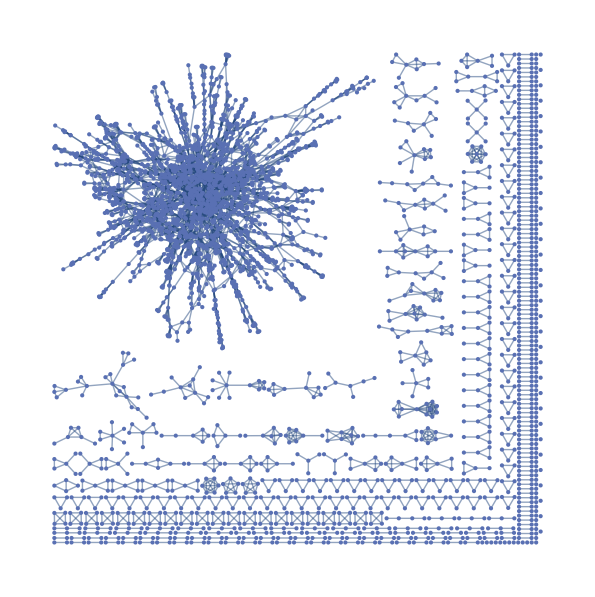

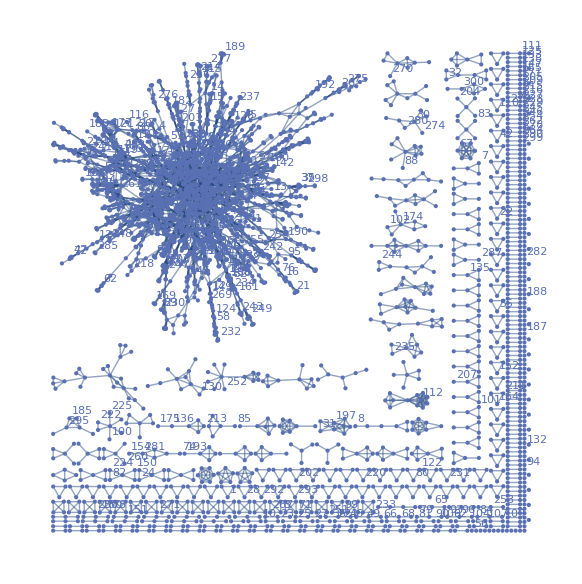

Cluster all authors into groups based on connectivity

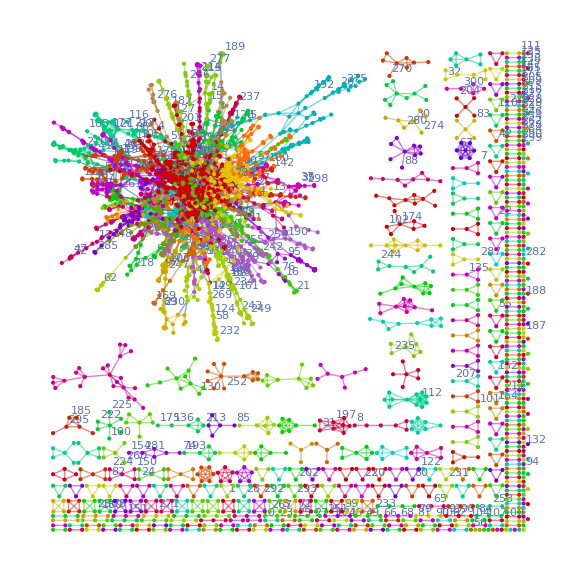

-Graphics-

```mathematica
data1="./Documents/data_analysis/Jiashun/coauthorship/coauthorAdj.txt";
data2="./Documents/data_analysis/Jiashun/coauthorship/coauthorAdjGiant.txt";
data3="./Documents/data_analysis/Jiashun/coauthorship/coauthorAdjThreshGiant.txt";
names2="./Documents/data_analysis/Jiashun/coauthorship/authorListCoauthorGiant.txt";
names3="./Documents/data_analysis/Jiashun/coauthorship/authorListCoauthorThreshGiant.txt";
data=data1;
(*names=names3;*)
Style["The data used is "<>data,Blue,Large]
adjMatrix=ReadList[data,Number ,RecordLists->True];
(*nameList=ReadList[names,String];*)
(*Dimensions[adjMatrix]
Dimensions[nameList]
adjMatrix[[1]]*)
Style["Here are adjacency graph without numbers, with numbers (*and with names,*) respectively", Blue, Large]
adjGraphPoint=AdjacencyGraph[adjMatrix]
adjGraphNumber=AdjacencyGraph[adjMatrix,VertexLabels->"Name"]
(*adjGraphName=AdjacencyGraph[adjMatrix,VertexLabels->Table[i->nameList[[i]],{i,1,Length[nameList]}]]*)
adjGraph=adjGraphNumber;
(*Style["\"Top\" 10 authors (from less to greater) are: ", Blue, Large]
 degree=DegreeCentrality[adjGraph];
(*Sort[degree]*)
(* top n, from less to greater *)
Ordering[degree,-10];
nameList[[%]]*)
groups=FindGraphCommunities[adjGraph];
(*Dimensions[groups]*)
Style["Cluster all authors into groups based on connectivity ",Blue,Large]
HighlightGraph[adjGraph,Subgraph[adjGraph,#]& /@groups]
CommunityGraphPlot[adjGraph,groups]
(*Table[
Print@Style["Group "<>ToString[j],Magenta,Large];
Print[nameList[[groups[[j]] ]]];
Print[Style["\"Top\" 2 authors in Group "<>ToString[j],Orange,Medium]];
degreej=degree[[groups[[j]]]];
groupTopIndex=Ordering[degreej,-2];
groupTop=groups[[j]][[groupTopIndex]];
Print[nameList[[groupTop]]],
{j,1,Length[groups]}];*)
```